```mathematica
D[U[x,t],x]
```

U^(1,0)[x,t]

```mathematica
D[f[x,t],x]==D[f[x,t],{t,2}]
```

f^(1,0)[x,t]==f^(0,2)[x,t]

```mathematica
DSolve[Derivative[1,0][f][x,t]==Derivative[0,2][f][x,t],{f[x,t],f[x,t]},{t,x}]
```

DSolve[f^(1,0)[x,t]==f^(0,2)[x,t],{f[x,t],f[x,t]},{t,x}]

```mathematica
DSolve[{Derivative[1,0][f][x,t]==Derivative[0,2][f][x,t],f[x,0]==Sin[x]},{f[x,t],f[x,t]},{t,x}]
```

DSolve[{f^(1,0)[x,t]==f^(0,2)[x,t],f[x,0]==Sin[x]},{f[x,t],f[x,t]},{t,x}]

```mathematica
DSolve[{Derivative[1,0][f][x,t]==Derivative[0,2][f][x,t],f[x,0]==Sin[x]},{f[x,t]},{t,x}]
```

DSolve[{f^(1,0)[x,t]==f^(0,2)[x,t],f[x,0]==Sin[x]},{f[x,t]},{t,x}]

```mathematica
DSolve[{Derivative[1,0][f][x,t]==Derivative[0,2][f][x,t],f[x,0]==Sin[x]},{f[x,t]},{x,t}]
```

DSolve[{f^(1,0)[x,t]==f^(0,2)[x,t],f[x,0]==Sin[x]},{f[x,t]},{x,t}]

```mathematica
DSolveValue[{Derivative[1,0][f][x,t]==Derivative[0,2][f][x,t],f[x,0]==Sin[x]},{f[x,t]},{x,t}]
```

$Aborted

```mathematica
DSolve[{D[f[x,t],t]==D[f[x,t],{x,2}],f[x,0]==Sin[x]},{f[x,t]},{x,t}]
```

{{f[x,t]→ⅇ^-t Sin[x]}}

```mathematica
DSolve[{D[f[x,t],t]==D[f[x,t],{x,2}],f[x,0]==g[x]},{f[x,t]},{x,t}]
```

{{f[x,t]→Integrate[(ⅇ^(-(x-K[1])^2/(4 t)) g[K[1]])/(2 √π √t),{K[1],-∞,∞},Assumptions→t>0]}}

```mathematica
FullSimplify[
DSolve[{D[f[x,t],t]==D[f[x,t],{x,2}],f[x,0]==g[x]},{f[x,t]},{x,t}],{f[x,t],x,t,g[x]}∈Reals]
```

{{f[x,t]→Integrate[(ⅇ^(-(x-K[1])^2/(4 t)) g[K[1]])/(2 √π √t),{K[1],-∞,∞},Assumptions→t>0]}}

```mathematica
FullSimplify[
x[n+1]==x[n]x[n-1]-1,{n,x[n]}∈Reals]
```

x[-1+n] x[n]==1+x[1+n]

```mathematica
Reduce[x[-1+n] x[n]==1+x[1+n]]
```

(x[1+n]==-1&&x[n]==0)||(x[n]≠0&&x[-1+n]==(1+x[1+n])/x[n])

```mathematica
FullSimplify[
RSolve[{x[n+1]==x[n]x[n-1]-1,x[1]==1},{x[n]},n],{n,x[n]}∈Reals]
```

RSolve[{x[-1+n] x[n]==1+x[1+n],x[1]==1},{x[n]},n]

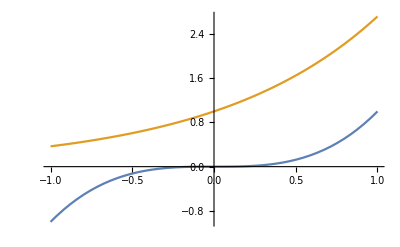

```mathematica
Plot[{
x^3,
Exp[x]
},{x,-1,1},
PlotRange->Full]
```

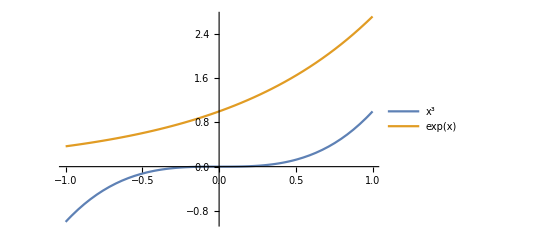

```mathematica
Plot[{
x^3,
Exp[x]
},{x,-1,1},
PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
Manipulate[
Plot[{
x^3,
Exp[x],
a x^3+(1-a)Exp[x]
},{x,-1,1},
PlotRange->Full,PlotLegends->"Expressions"],
{a,0,1}]
```

```mathematica
Integrate[a x^3+(1-a)Exp[x],{x,-1,1}]
```

-((-1+a) (-1+ⅇ^2))/ⅇ

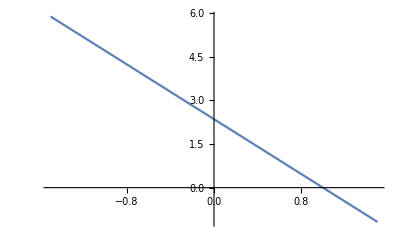

```mathematica
Plot[-((-1+a) (-1+ⅇ^2))/ⅇ,{a,-1.5,1.5}]
```

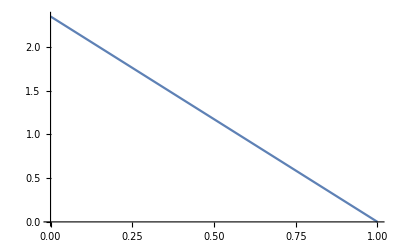

```mathematica
Plot[-((-1+a) (-1+ⅇ^2))/ⅇ,{a,0,1}]
```

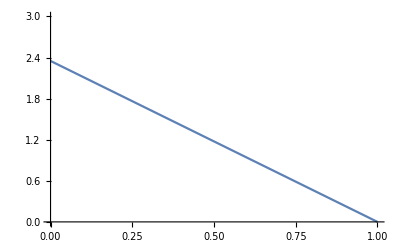

```mathematica
Plot[-((-1+a) (-1+ⅇ^2))/ⅇ,{a,0,1},PlotRange->{0,3}]
```

```mathematica
Integrate[√(1+D[a x^3+(1-a)Exp[x],x]^2),{x,-1,1}]
```

$Aborted

```mathematica
D[a x^3+(1-a)Exp[x],x]^2
```

((1-a) ⅇ^x+3 a x^2)^2

```mathematica
Integrate[√(1+((1-a) ⅇ^x+3 a x^2)^2),{x,-1,1}]
```

$Aborted

```mathematica
FullSimplify[
√(1+((1-a) ⅇ^x+3 a x^2)^2),{a,x}∈Reals]
```

√(1+((-1+a) ⅇ^x-3 a x^2)^2)

```mathematica
f[x+a]==f[x]+∫_x^(x+a) f'[x]ⅆx
```

f[a+x]==f[x]+∫_x^(a+x) f'[x]ⅆx

```mathematica
f[x+a]==f[x]+f'[x]a
```

```mathematica
Manipulate[
Plot[{
x,
Exp[x],
a x+(1-a)Exp[x]
},{x,-1,1},
PlotRange->Full,PlotLegends->"Expressions"],
{a,0,1}]
```

```mathematica
Manipulate[
Plot[{
x,
Exp[x],
a x+(1-a)Exp[x]
},{x,-1,1},
PlotRange->Full,PlotLegends->"Expressions"],
{a,0,1}]
```

```mathematica
Manipulate[
Plot[{
x,
Exp[x],
a x+(1-a)Exp[x]
},{x,-1,1},
PlotRange->{-3,3},PlotLegends->"Expressions"],
{a,0,1}]
```

```mathematica
Manipulate[
Plot[{
x,
Exp[x],
a x+(1-a)Exp[x],
x^b Exp[x]^(1-b)
},{x,-1,1},
PlotRange->{-3,3},PlotLegends->"Expressions"],
{a,0,1},{b,0,1}]
```

```mathematica
Integrate[√(1+D[a x+(1-a)Exp[x],x]^2),{x,-1,1}]
```

$Aborted

```mathematica
Manipulate[
Plot[{
x,
x^2,
a x+(1-a)x^2,
x^b (x^2)^(1-b)
},{x,-1,1},
PlotRange->{-3,3},PlotLegends->"Expressions"],
{a,0,1},{b,0,1}]
```

```mathematica
Integrate[√(1+D[a x+(1-a)x^2,x]^2),{x,-1,1}]
```

ConditionalExpression[-((2-3 a) √(5-12 a+9 a^2)+ArcSinh[2-3 a])/(4 (-1+a))+((-2+a) √(5-4 a+a^2)-ArcSinh[2-a])/(4 (-1+a)),(Re[a]/(2-2 Re[a])≥1||Re[a]/(-2+2 Re[a])≥1||Im[a]^2/(-1+Re[a])^2≤1)&&(1+1/Im[a/(-1+a)]≠Re[a]||Im[1/(-1+a)]+Re[a/(-1+a)]≥2||2+Im[1/(-1+a)]≤Re[a/(1-a)])&&(Im[a/(-1+a)]≠Re[1/(-1+a)]||Im[a/(1-a)]+Re[1/(-1+a)]≠0||2+Re[a/(1-a)]<Im[1/(-1+a)]||2+Im[1/(-1+a)]+Re[a/(-1+a)]<0)]

```mathematica
FullSimplify[
Integrate[√(1+D[a x+(1-a)x^2,x]^2),{x,-1,1}],a∈Reals]
```

ConditionalExpression[-(-(-2+a) √(5+(-4+a) a)+(2-3 a) √(5+3 a (-4+3 a))+ArcSinh[2-3 a]+ArcSinh[2-a])/(4 (-1+a)),(a≠1+1/Im[a/(-1+a)]||Im[1/(-1+a)]+a Re[1/(-1+a)]≥2||2+Im[1/(-1+a)]≤a Re[1/(1-a)])&&(a Im[1/(-1+a)]≠Re[1/(-1+a)]||a Im[1/(1-a)]+Re[1/(-1+a)]≠0||2+a Re[1/(1-a)]<Im[1/(-1+a)]||2+Im[1/(-1+a)]+a Re[1/(-1+a)]<0)]

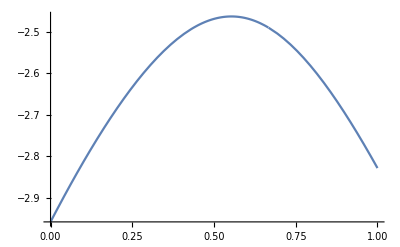

```mathematica
Plot[
(-(-2+a) √(5+(-4+a) a)+(2-3 a) √(5+3 a (-4+3 a))+ArcSinh[2-3 a]+ArcSinh[2-a])/(4 (-1+a)),
{a,0,1}]
```

```mathematica
FindMaximum[
(-(-2+a) √(5+(-4+a) a)+(2-3 a) √(5+3 a (-4+3 a))+ArcSinh[2-3 a]+ArcSinh[2-a])/(4 (-1+a)),
{a,.6}]
```

{-2.46373,{a→0.55329}}

```mathematica
Manipulate[
Plot[{
x,
x^2,
a x+(1-a)x^2,
x^b (x^2)^(1-b)
},{x,-1,1},
PlotRange->{-3,3},PlotLegends->"Expressions"],
{a,0,1},{b,0,1}]
```

```mathematica
f'[x]==λ f[x]
```

f'[x]==λ f[x]

```mathematica
DSolve[f'[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x λ) C[1]}}

```mathematica
ReflectionTransform[f[x]]
```

ReflectionTransform[f[x]]

```mathematica
ReflectionTransform[{x,f[x]}]
```

TransformationFunction[((Abs[x]^2+Abs[f[x]]^2-2 x Conjugate[x])/(Abs[x]^2+Abs[f[x]]^2) | -(2 x Conjugate[f[x]])/(Abs[x]^2+Abs[f[x]]^2) | 0
-(2 Conjugate[x] f[x])/(Abs[x]^2+Abs[f[x]]^2) | (Abs[x]^2+Abs[f[x]]^2-2 Conjugate[f[x]] f[x])/(Abs[x]^2+Abs[f[x]]^2) | 0
0 | 0 | 1)]

```mathematica
FullSimplify[
ReflectionTransform[{x,f[x]}]{x,f[x]}∈Reals]
```

(x TransformationFunction[((-x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x]+Conjugate[f[x]] f[x]) | -(2 x Conjugate[f[x]])/(x Conjugate[x]+Conjugate[f[x]] f[x]) | 0
-(2 Conjugate[x] f[x])/(x Conjugate[x]+Conjugate[f[x]] f[x]) | (x Conjugate[x]-Conjugate[f[x]] f[x])/(x Conjugate[x]+Conjugate[f[x]] f[x]) | 0
0 | 0 | 1)]|f[x] TransformationFunction[((-x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x]+Conjugate[f[x]] f[x]) | -(2 x Conjugate[f[x]])/(x Conjugate[x]+Conjugate[f[x]] f[x]) | 0
-(2 Conjugate[x] f[x])/(x Conjugate[x]+Conjugate[f[x]] f[x]) | (x Conjugate[x]-Conjugate[f[x]] f[x])/(x Conjugate[x]+Conjugate[f[x]] f[x]) | 0
0 | 0 | 1)])∈ℝ

```mathematica
FullSimplify[
ReflectionTransform[{x,f[x]}]=={x,f[x]},{x,λ f[x]}∈Reals]
```

TransformationFunction[((-x^2+Abs[f[x]]^2)/(x^2+Abs[f[x]]^2) | -(2 x Conjugate[f[x]])/(x^2+Abs[f[x]]^2) | 0
-(2 x f[x])/(x^2+Abs[f[x]]^2) | (x^2-Abs[f[x]]^2)/(x^2+Abs[f[x]]^2) | 0
0 | 0 | 1)]=={x,f[x]}

```mathematica
FullSimplify[
ReflectionTransform[{x,f[x]}]=={x,λ f[x]},{x,λ,f[x]}∈Reals]
```

TransformationFunction[((-x^2+f[x]^2)/(x^2+f[x]^2) | -(2 x f[x])/(x^2+f[x]^2) | 0
-(2 x f[x])/(x^2+f[x]^2) | (x^2-f[x]^2)/(x^2+f[x]^2) | 0
0 | 0 | 1)]=={x,λ f[x]}

```mathematica
Solve[
FullSimplify[
ReflectionTransform[{x,f[x]}]=={x,λ f[x]},{x,λ,f[x]}∈Reals],{λ}]
```

{}

```mathematica
√(1+f'[x]^2)
```

√(1+f'[x]^2)

```mathematica
D[√(1+f'[x]^2),f[x]]-D[D[√(1+f'[x]^2),f'[x]],x]==0
```

(f'[x]^2 f''[x])/((1+f'[x]^2)^(3/2))-f''[x]/(√(1+f'[x]^2))==0

```mathematica
DSolve[(f'[x]^2 f''[x])/((1+f'[x]^2)^(3/2))-f''[x]/(√(1+f'[x]^2))==0,{f[x],f[x]},{x}]
```

{{f[x]→C[1]+x C[2]}}

```mathematica
f'[f[x]]==x
```

f'[f[x]]==x

```mathematica
DSolve[f'[f[x]]==x,{f[f[x]]},{x}]
```

DSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in f[f[x]] should literally match the independent variables.

DSolve[f'[f[x]]==x,{f[f[x]]},{x}]

```mathematica
DSolve[f'[f[x]]==x,{f[x]},{x}]
```

DSolve::nestdv: The expression f[x] has nested dependent variables.

DSolve[f'[f[x]]==x,{f[x]},{x}]

```mathematica
(ϕ-1)^(ϕ-1)x^ϕ
```

x^ϕ (-1+ϕ)^(-1+ϕ)

```mathematica
Manipulate[Plot[x^ϕ (-1+ϕ)^(-1+ϕ),{x,-10.,10.}],{ϕ,-10.,10.}]
```

```mathematica
D[x^ϕ (-1+ϕ)^(-1+ϕ),x]
```

x^(-1+ϕ) (-1+ϕ)^(-1+ϕ) ϕ

```mathematica
Manipulate[Plot[x^(-1+ϕ) (-1+ϕ)^(-1+ϕ) ϕ,{x,-10.,10.}],{ϕ,-6.,6.}]
```

```mathematica
{a,b,c}
```

{a,b,c}

```mathematica
Outer[distance,{a,b,c}]
```

{distance[a],distance[b],distance[c]}

```mathematica
Outer[distance,{a,b,c},{a,b,c}]
```

{{distance[a,a],distance[a,b],distance[a,c]},{distance[b,a],distance[b,b],distance[b,c]},{distance[c,a],distance[c,b],distance[c,c]}}

```mathematica
Subsets[Range@3]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Subsets@Range@3
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
distance[x_,y_]:=Abs[x-y]
```

```mathematica
Outer[distance,{a,b,c},{a,b,c}]
```

{{0,Abs[a-b],Abs[a-c]},{Abs[-a+b],0,Abs[b-c]},{Abs[-a+c],Abs[-b+c],0}}

```mathematica
Outer[distance,Range@3,Range@3]
```

{{0,1,2},{1,0,1},{2,1,0}}

```mathematica
Colorize[{{0,1,2},{1,0,1},{2,1,0}}]
```

-Graphics-

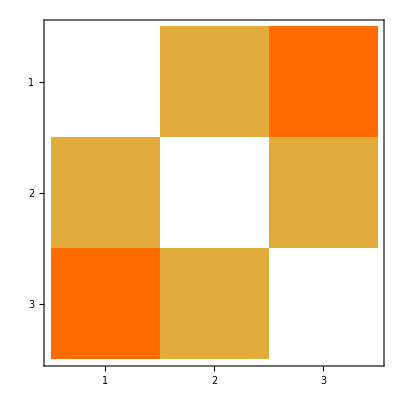

```mathematica
MatrixPlot[{{0,1,2},{1,0,1},{2,1,0}}]
```

```mathematica
{{0,1,2},{1,0,1},{2,1,0}} //MatrixForm
```

(0 | 1 | 2
1 | 0 | 1
2 | 1 | 0)

```mathematica
Grid@
{{0,1,2},{1,0,1},{2,1,0}}
```

0 | 1 | 2
1 | 0 | 1
2 | 1 | 0

```mathematica
Grid@
Prepend[
{{0,1,2},{1,0,1},{2,1,0}} ,
{1,2,3}]
```

1 | 2 | 3
0 | 1 | 2
1 | 0 | 1
2 | 1 | 0

```mathematica
Insert[Grid[{{1,2,3},{0,1,2},{1,0,1},{2,1,0}}],{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

1 | 2 | 3
0 | 1 | 2
1 | 0 | 1
2 | 1 | 0

```mathematica
f'[x]==1/x
```

f'[x]==1/x

```mathematica
DSolve[f'[x]==1/x,{f[x]},{x}]
```

{{f[x]→C[1]+Log[x]}}

```mathematica
DSolve[{f'[x]==f[x]},{f[x]},{x}]
```

{{f[x]→ⅇ^x C[1]}}